## Methods

```mathematica
headerList={"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
```

```mathematica
GetData[fileName0_]:=
Module[{file = fileName0,v},
v=Import[file];
v=StringSplit[v,"\t"];
v=StringSplit[v,"\n"];
v
]
```

```mathematica
CleanDataRecord[record0_]:=
Module[{record = record0,test},
test = StringSplit[#,","]&/@record;
test =Drop[test,1];
test=ToExpression/@test;
test=PrependTo[test,headerList];
test=Dataset[Map[AssociationThread[First[test],#]&,Rest[test]]];
test
]
```

```mathematica
DisplayData[dataList0_]:=
Module[{l=dataList0,gg,a,b,c,d},
row[text_,plot_]:=Row[{text,plot},Alignment->Center];
labels=Text[Style[#,18]]&/@{"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
a=ListLinePlot[l[[All,1]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];
b=ListLinePlot[l[[All,2]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];
c=ListLinePlot[l[[All,3]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];
d=ListLinePlot[l[[All,4]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];
gg2=GraphicsGrid[Partition[row@@@Thread[{labels,{a,b,c,d}}],4],Spacings->{10,20},Frame->None,ImageSize->Full];
gg2
]
```

## Execute

4

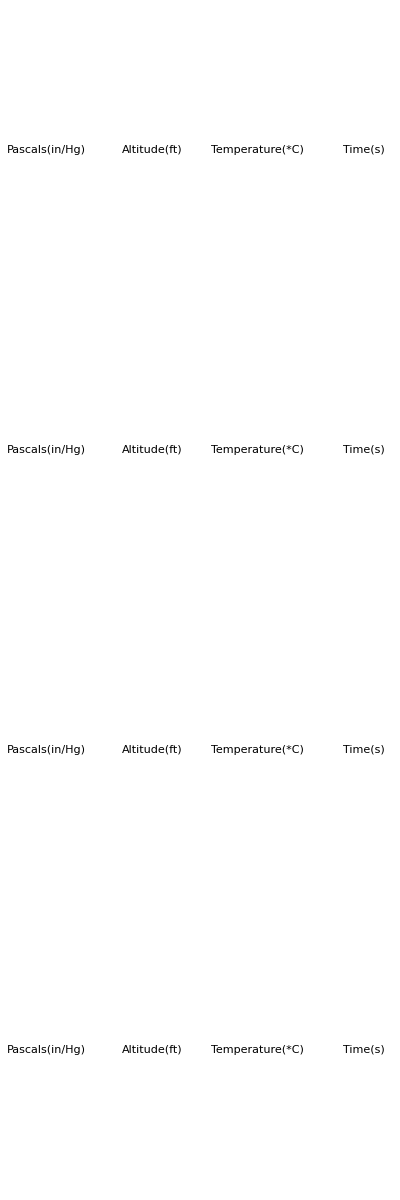

```mathematica
SetDirectory[NotebookDirectory[]];
data=GetData["RC.TXT"];
cleanData=CleanDataRecord/@data;
cleanData//Length
graphs=DisplayData/@cleanData;
graphs//TableForm
```